# DirectionParametricPlot

Create a parametric plot of a curve in the plane with direction indicated by arrowheads and color: https://resources.wolframcloud.com/FunctionRepository/resources/DirectionParametricPlot/

## Definition

```mathematica
DirectionParametricPlot[fun_, {t_, t0_, t1_}, opts___?OptionQ] := 
	Module[{x,y,z,funl, fp, aheads, asize, anumber, color, pp, gr, vars, arrow, data, dt = N[t1 - t0], ps, psdata, dpts, plotfun, plotrange}, 
	funl = ReleaseHold[Hold[fun] /. {Integrate -> NIntegrate, Tooltip[a_]->a}]//Quiet;
	If[VectorQ[funl],funl = ReleaseHold[{Hold[funl]}]];
	If[Head[funl] === Piecewise, funl = {funl}];
	If[MatrixQ[First[funl]], funl = Flatten[funl,1]];
	If[Not[MatrixQ[funl/.t->t0]] & , Return[Message[dpp::improperinput]]];
        {aheads, anumber, color} = 
	    {"DrawArrowheads", "ArrowNumber", ColorFunction} /. {opts} /.  
               Options[DirectionParametricPlot];		
     If[anumber <= 0, aheads = False];
     {ps,asize}=AppendOptions[DirectionParametricPlot,{PlotStyle,"ArrowSize"}, Length[funl],opts]; 
asize = If[Head[#] === Symbol,{#},{.05#}] & /@ (Last/@asize);
     vars = {x,y};
     arrow = (Arrow[#]&); 

     If[Not[FreeQ[ps, RGBColor[_,_,_] | Hue[_] | GrayLevel[_]]], color =None];
     If[MatchQ[color, Automatic],  
                 color = Function[Flatten[{vars,t}]//Evaluate, Hue[.9 t]]];		
     aheads = 
	If[aheads,fp = D[funl, t];
          If[FreeQ[fp, Derivative, Infinity], 			
	If[color === None, psdata = 
 {RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051],
RGBColor[0.560181, 0.691569, 0.194885], RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
		RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], RGBColor[0.571589, 0.586483, 0.], 
		RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609, 0.52200666434, 0.85], 
		RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], RGBColor[0.736782672705901, 0.358, 0.5030266573755369], 
		RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]
		};
	     ps = MapThread[Flatten[{#1,#2}]&,{psdata[[1;;Length[funl]]],ps}];
	     ps1 = DeleteCases[ ps, Thickness[_]|Tube[_], Infinity]; 
data = Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], {t, t0 + dt/anumber, t1, dt/(anumber+.0001)}];
data = Map[MapThread[Flatten[{Arrowheads[Last[Flatten[{#2}]]],#1,#3}]&,{ps1,asize,#}]&,data],
			
acolor= Table[color[Sequence@@Flatten[{vars,(t - t0)/dt}]],{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
asizes=Map[Arrowheads,asize,{2}]; 
arrows=Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], 
										{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
data=MapThread[{#1,#2}&,{acolor,(Transpose[Flatten/@{asizes,#}]&/@arrows)}]];
              Select[data, FreeQ[#, Indeterminate, Infinity] &, Infinity],
              Message[dpp::noderiv];{}],{}];

Show[	
	ParametricPlot[funl//Evaluate, {t, t0, t1}, ColorFunction -> color, PlotStyle -> ps,
				Sequence @@ FilterRules[{opts}, Options[ParametricPlot]] // Evaluate], 
	Graphics[aheads],  Sequence@@FilterRules[{opts},Options[Graphics]]//Evaluate,
   PlotRangePadding->Scaled[.04]]
	]

Options[DirectionParametricPlot]=
{"ArrowNumber"->15,"ArrowSize"->Large,ColorFunction->Automatic,"DrawArrowheads"->True,PlotStyle->Automatic};

dpp::noderiv="Mathematica was unable to find the derivative which is used to produce the arrowheads. Plotting will proceed without arrowheads. ";

dpp::improperinput="The input function is not a vector or a list of vectors. ";
AppendOptions[command_Symbol,options_,rest__]:=AppendOptions[command,{options},rest]
AppendOptions[command_Symbol,{options__},number_?(IntegerQ[#]&&NonNegative[#]&),opts___Rule]:=AppendOptions[command,{options},Table[number,{Length[{options}]}],opts]
AppendOptions[command_Symbol,{options__},numbers_?(VectorQ[#,(IntegerQ[#]&&NonNegative[#])&]&),opts___Rule]:=Module[{defaultstyles,userstyles,lengths,newstyles},defaultstyles={options}/.Options[command];
userstyles={options}/.{opts}/.Options[command];
userstyles=(If[ListQ[#],#,{#}]&/@userstyles)/.{}->{{}};
lengths=Length/@userstyles;
newstyles=MapThread[MapThread[Flatten[{#1,#2}]&,{Table[#1,{#2}],#3}]&,{defaultstyles,lengths,userstyles}];
newstyles=MapThread[Join[Flatten[Table[#1,{Floor[#2/#3]}],1],Take[#1,Mod[#2,#3]]]&,{newstyles,numbers,lengths}];
With[{temp=DeleteCases[newstyles,Automatic,Infinity]},If[Length[{options}]===1,First[temp],temp]]]
```

## Documentation

### Usage

DirectionParametricPlot[{f_x,f_y},{t,t_min,t_max}]

generates a parametric plot of a curve {f_x,f_y} whose x- and y-coordinates f_x and f_y are functions of t and with the direction of the curve indicated by color and arrowheads.

### Details & Options

The following options are supported:

"ArrowNumber" | 15 | number of arrowheads to include in the plot
"ArrowSize" | Large | size of the arrowheads
ColorFunction | Automatic | specify the color function
"DrawArrowheads" | True | whether to include the arrowheads in the plot
PlotStyle | Automatic | style to be applied to the curve

## Examples

### Basic Examples

A curve with direction indicated by color and arrowheads:

```mathematica
DirectionParametricPlot[{Cos[t] Cos[2 t],Sin[t]},{t,0,2 π}]
```

-Graphics-

## Weyl

```mathematica
Solve[(2 a2 ky+kz-a2^2 kz)/(1+a2^2)==μ,ky]//FullSimplify
```

{{ky→((-1+a2^2) kz+μ+a2^2 μ)/(2 a2)}}

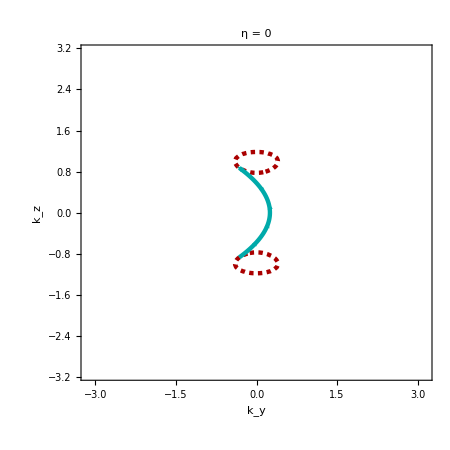

```mathematica
lim=π;mu=0.4;kw=1;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};

a2=-2;

pp=DirectionParametricPlot[{((-1+a2^2) (kz^2-kw^2)+mu+a2^2 mu)/(2 a2),kz},{kz,-0.9 ,0.9},"ArrowSize"->Medium,PlotRange->{{-lim ,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},Chop[(-1+a2^2) ky+2 a2 (kz^2-kw^2)]>0 ],PlotStyle->Directive[Darker[Cyan],Thickness[th]],"ArrowNumber"->5];
(***************)
kx=0;fs=ContourPlot[(kz^2-kw^2)^2+kx^2+ky^2==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]],PlotLegends->Automatic];
pl1=Show[fs,pp,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"η = 0",20,FontFamily->"TexMaths Symbols",Brown,Bold](**)]
Clear[a2,vz,vp,kx];
```

### Options

#### ArrowSize

The option "ArrowSize"->1 corresponds (roughly) to the default "ArrowSize"->Large:

```mathematica
DirectionParametricPlot[{Cos[t] Cos[2 t],Sin[t]},{t,0,2 π},"ArrowSize"->1]
```

-Graphics-

The same curve with smaller arrowheads:

```mathematica
DirectionParametricPlot[{Cos[t] Cos[2 t],Sin[t]},{t,0,2 π},"ArrowSize"->Medium]
```

-Graphics-

#### ArrowNumber

Plot more arrowheads:

Suppress the arrowheads by setting "ArrowNumber" to zero:

#### DrawArrowheads

Suppress the arrowheads:

```mathematica
DirectionParametricPlot[{Cos[t] Cos[2 t],Sin[t]},{t,0,2 π},"DrawArrowheads"->False]
```

-Graphics-

#### PlotStyle

Setting PlotStyle to a color plots the curve in that color:

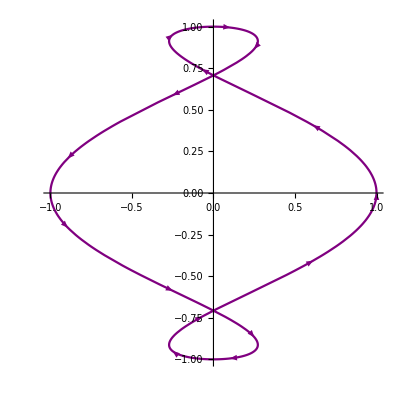

```mathematica
DirectionParametricPlot[{Cos[t] Cos[2 t],Sin[t]},{t,0,2 π},PlotStyle->Purple]
```

Plot two curves with a different style as well as a different size arrowhead for each curve:

```mathematica
DirectionParametricPlot[{{Cos[t] Cos[2 t],Sin[t]},{Cos[t] Cos[4 t],Sin[t]}},{t,0,2 π},PlotStyle->{Thickness[.01],Thickness[.015]},"ArrowSize"->{1,1.3}]
```

-Graphics-

Other settings for PlotStyle will not affect the automatic coloring:

```mathematica
DirectionParametricPlot[{Cos[t] Cos[4 t],Sin[t]},{t,0,2 π},PlotStyle->Thickness[.01]]
```

-Graphics-

For multiple curves, if just one style is specified, it is applied to both curves:

```mathematica
DirectionParametricPlot[{{Cos[t],2 Sin[t]},{Cos[t],Sin[t]}},{t,0,2 π},PlotStyle->Thickness[.017]]
```

-Graphics-

#### ColorFunction

Change the color function:

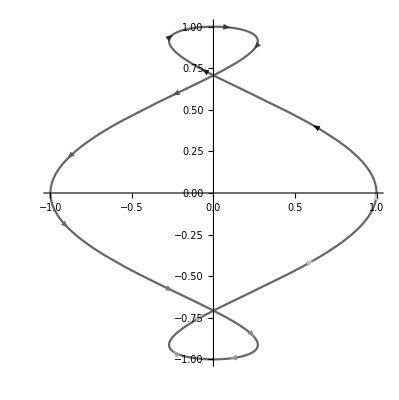

```mathematica
DirectionParametricPlot[{Cos[t] Cos[2 t],Sin[t]},{t,0,2 π},ColorFunction->Function[{x,y,t},GrayLevel[.8t]]]
```

#### PlotLegends

Since PlotLegends depends on the color of the curve, they will not work unless ColorFunction is set to None or the specifications for PlotStyle contain a color:

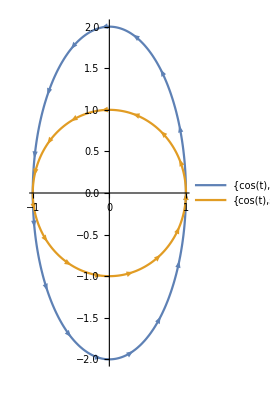

```mathematica
DirectionParametricPlot[{{Cos[t],2 Sin[t]},{Cos[t],Sin[t]}},{t,0,2 π},ColorFunction->None,PlotLegends->"Expressions"]
```

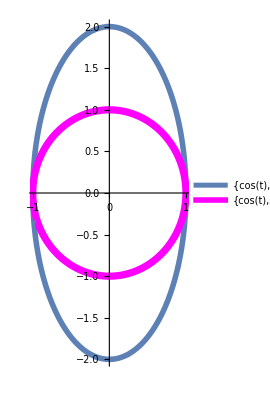

```mathematica
DirectionParametricPlot[{{Cos[t],2 Sin[t]},{Cos[t],Sin[t]}},{t,0,2 π},PlotStyle->{Thickness[.01],{Magenta,Thickness[.013]}},PlotLegends->"Expressions"]
```

### Properties and Relations

Without DirectionParametricPlot, it is difficult to tell how the curve is traced out:

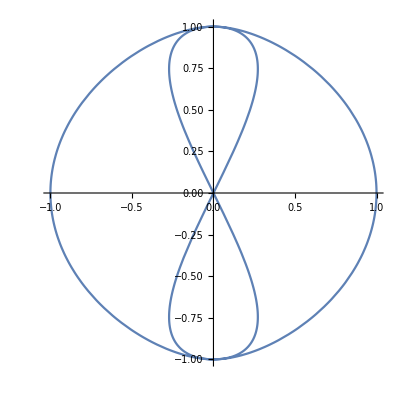

```mathematica
ParametricPlot[{Sin[t]Cos[2t],2Sin[t]Cos[t]},{t,0,2π}]
```

Using DirectionParametricPlot, it is easy to see how the curve is traced out:

```mathematica
DirectionParametricPlot[{Sin[t]Cos[2t],2Sin[t]Cos[t]},{t,0,2π}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Dennis M Schneider

### Keywords

curves

colors

arrows

directions

parameterized curve

parametric plot

direction

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

ParametricPlot

ParametricPlot3D

### Related Resource Objects

DirectionParametricPlot3D

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

## Submission Notes